### Wprowadzenie wartości dla prędkości początkowej cząstki α ( "v_αo" ) oraz mas: cząstki α ( "m_α" ), uranu ( "m_u" ) i węgla ( "m_c" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
mα=4;                                  (* a.j.m. *)
```

```mathematica
mu=238;                             (* a.j.m. *)
```

```mathematica
mc=12;                                (* a.j.m. *)
```

```mathematica
vαo=10^3;                          (* m/s*)
```

### Wprowadzenie zależności pomiędzy składowymi stycznymi prędkości cząstki α przed ( "v_αos" ) i po zderzeniu ( "v_αs" ) oraz wypisanie wzorów na składową styczną ( “v_αos” ) i normalną ( “v_αon” ) prędkości cząstki α przed zderzeniem.

```mathematica
vαs=vαos;
vαos=vαo×Sin[ϕ ];
 vαon=vαo×Cos[ϕ ];
```

### Wprowadzenie zależności pomiędzy prędkością cząstki α po zderzeniu ( "v_α" ) a jej składowymi styczną ( "v_αs" ) i normalną ( "v_αn" ).

```mathematica
vα=√(vαs^2+vαn^2);
```

### Wprowadzenie wzorów na energie kinetyczne: początkową cząstki α ( "E_kαo" ), końcową cząstki α ( "E_kα" ) i końcową jądra ( "E_kj" ). Symbole "v_αon", "v_jn" oznaczają odpowiednio składowe normalne prędkości cząstki α przed zderzeniem i jądra po zderzeniu.

```mathematica
Ekαo=(mα×vαo^2)/2
Ekα=(mα×vα^2)/2
Ekj=(mj×vjn^2)/2;
```

2000000

2 (vαn^2+1000000 Sin[ϕ]^2)

### Wprowadzenie wzorów na składowe normalne pędów: początkowego cząstki α ( "p_αon" ), końcowego cząstki α ( "p_αn" ) i końcowego jądra ( "p_jn" ).

```mathematica
pαon=mα×vαon;
pαn=mα×vαn;
pjn=mj×vjn;
```

### Obliczenie składowych normalnych prędkości końcowych jądra i cząstki α z zasad zachowania energii i pędu.

```mathematica
A=Solve[{Ekαo==Ekα+Ekj,pαon==pαn+pjn},{vjn,vαn}]
```

{{vjn→0,vαn→1000 Cos[ϕ]},{vjn→(8000 Cos[ϕ])/(4+mj),vαn→-(1000 (-4+mj) Cos[ϕ])/(4+mj)}}

### Sporządzenie wykresów obrazujących zależność prędkości jądra uranu i cząstki α po zderzeniu od kąta zderzenia ( "ϕ" ).

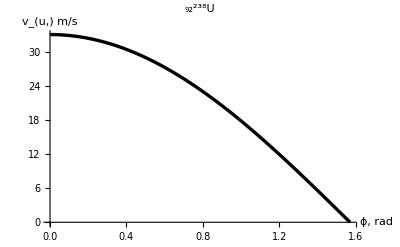

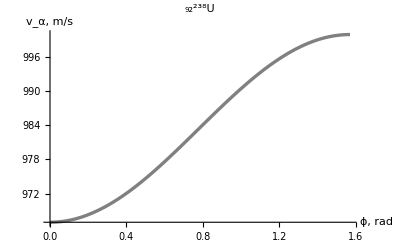

```mathematica
rys1=Plot[vjn/.A[[2,1]]/.mj->mu,{ϕ,0,π/2},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{"ϕ, rad ","v_(u,) m/s "},
PlotLabel->StyleForm["_92^238U",
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"]]
rys2=Plot[vα/.A[[2,2]]/.mj->mu,{ϕ,0,π/2},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{Gray,Thickness[0.006]},
AxesLabel->{"ϕ, rad ","v_α, m/s "},
PlotLabel->StyleForm[" _92^238U  ",
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"]]
```

### Sporządzenie wykresów obrazujących zależność prędkości jądra węgla i cząstki α po zderzeniu od kąta zderzenia ( "ϕ" ).

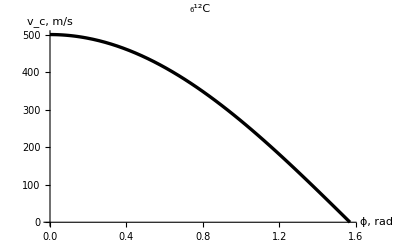

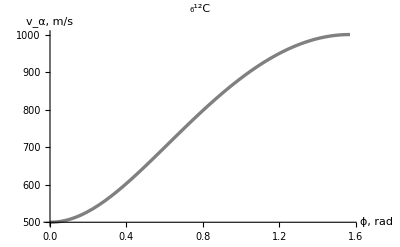

```mathematica
rys3=Plot[vjn/.A[[2,1]]/.mj->mc,{ϕ,0,π/2},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{"ϕ, rad ","v_c, m/s  "},
PlotLabel->StyleForm["  _6^12C  ",
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"]]
rys4=Plot[vα/.A[[2,2]]/.mj->mc,{ϕ,0,π/2},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{Gray,Thickness[0.006]},
AxesLabel->{"ϕ, rad ","v_α, m/s "},
PlotLabel->StyleForm["  _6^12C ",
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"]]
```